```mathematica
(*Basic code:*)
logspace[a_,b_,n_]:=10.^Range[a,b,(b-a)/n];

linspace[a_,b_,n_]:=Range[a,b,(b-a)/n];

tensor[a___]:=KroneckerProduct[a]

out[a_,b_]:=Outer[Times,a,Conjugate@b]

destroy[n_]:=Array[Sqrt[#1]KroneckerDelta[#1,#2-1]&,{n,n}]

create[n_]:=Array[Sqrt[#2]KroneckerDelta[#1,#2+1]&,{n,n}]

qeye[n_]:=Array[KroneckerDelta[#1,#2]&,{n,n}]

dag[a_]:=ConjugateTranspose[a]

c[a_,b_]:=a.b-b.a

ac[a_,b_]:=a.b+b.a

L[a_,rho_]:=2 a.rho.dag[a]-ac[dag[a].a,rho]

Rho[n_]:=Array[Subscript[r,#1,#2][t]&,{n,n}]

Lamb[n_,t_,tau_]:=Array[Subscript[La,#1,#2][t,tau]&,{n,n}]

LambSpec[n_,tau_]:=Array[Subscript[La,#1,#2][tau]&,{n,n}]

MatFromVec[vec_]:=With[{dim=Sqrt[Length[vec]]},Table[Take[vec,{i*dim+1,dim*(i+1)}],{i,0,dim-1}]]

fockbasis[dim_,n_]:=Array[KroneckerDelta[n+1,#1]*KroneckerDelta[#2,n+1]&,{dim,dim}]

Disp[n_,alp_]:=MatrixExp[alp(create[n]-destroy[n])]

MeqToLio[meq_]:=Normal[CoefficientArrays[Flatten@meq,Flatten@Rho[Length@meq]][[2]]]

nocc[nu_,beta_]:=1/(Exp[beta*nu]-1)

print[x___]:=Print[x]

ops[n_]:=Module[{sm, sp, a, adag},
sm = tensor[destroy[2],qeye[n]];
sp = dag[sm];
a = tensor[qeye[2],destroy[n]];
adag = dag@a;
N@{sm, sp, a, adag}]

 
JUD[w_, alp_, w0_, Gam_]:=(alp × Gam × w0^2 w)/((w^2-w0^2)^2+Gam^2 w^2)

IBMintegrand[t_,w_,alp_,w0_,Gam_, beta_]:= JUD[w, alp, w0, Gam]/w^2((1-Cos[w t])×Coth[(beta w)/2]+ⅈ Sin[w t])

Gfunc[t_, eps_, alp_, w0_, Gam_, beta_]:= Exp[ⅈ (eps (*- 1.5707963267948963 alp*))t] Exp[-NIntegrate[Evaluate@IBMintegrand[t, w, alp, w0, Gam, beta],{w,0,∞},
Method->{Automatic,"SymbolicProcessing"->False},AccuracyGoal->6,MaxRecursion->20]]  



RhoSolve[lio_,inn_,tend_]:=Module[{dim,rho,meq,Rho0,sol},
dim=Sqrt[Length@lio];
rho=Rho[dim];
meq=Thread[Flatten[D[rho,t]]==(lio.Flatten[rho])];
Rho0=Thread[Flatten[rho/.t->0]==Flatten[inn]];
sol=AbsoluteTiming[NDSolveValue[Flatten@{meq,Rho0},Diagonal@rho,{t,0,tend},Method->{"EquationSimplification"->"Solve"}]];
print["Took me ",sol[[1]]/60," minutes to integrate the master equation."];
sol⟦2⟧]



RhoVecSolve[lio_,inn_,tend_]:=Module[{dim,rho,meq,Rho0,sol},
sol=AbsoluteTiming[NDSolveValue[Flatten@{ρ'[t] == lio.ρ[t],ρ[0]==Flatten[inn]},ρ,{t,0,tend},AccuracyGoal->8]];
print["Took me ",sol[[1]]/60," minutes to integrate the master equation."];
sol⟦2⟧]

RhoSteady[lio_]:=Module[{dim,rho, meq, steady},
dim=Sqrt[Length@lio];
rho  = Rho[dim];
meq = Append[Thread[0==(lio.Flatten[rho])],Tr[rho]==1];
steady = rho/.First[NSolve[meq, Flatten@rho]];
steady]
```

```mathematica
JEM[w_, eps_, Gam0_]:=Gam0/(2π eps^3)w^3

PhotDissInc[Ham_, eps_, Gam0_, TEM_]:=Module[
{dim, vals, vecs, lam, sm, sp, O1, O2, O3, O4,diss},

(*Dimension of the space*)
dim = (Length@Ham)/2;

(*Find eigenvalues and eigenvectors of Hamiltonian*)
{vals, vecs} = Eigensystem@Ham;

(*Construct Eigenvalue difference array*) 
lam = Table[ii-jj, {ii,vals}, {jj,vals}];

sp = tensor[create[2], qeye[dim]];
sm = tensor[destroy[2], qeye[dim]];

O1 = Sum[
If[lam⟦ii,jj⟧==0, 0,
HeavisideTheta[lam⟦ii,jj⟧]×π×JEM[Abs@lam⟦ii,jj⟧, eps, Gam0]nocc[Abs@lam⟦ii,jj⟧, 1/TEM]]
×(Conjugate[vecs⟦ii⟧].sp.vecs⟦jj⟧)×out[vecs⟦ii⟧, vecs⟦jj⟧], 
{ii,1,Length@vals}, 
{jj,1,Length@vals}
];


O2 = Sum[
If[lam⟦ii,jj⟧==0, 0,
HeavisideTheta[lam⟦ii,jj⟧]×π×JEM[Abs@lam⟦ii,jj⟧, eps, Gam0](nocc[Abs@lam⟦ii,jj⟧, 1/TEM] + 1)]
×(Conjugate[vecs⟦ii⟧].sp.vecs⟦jj⟧)×out[vecs⟦ii⟧, vecs⟦jj⟧], 
{ii,1,Length@vals}, 
{jj,1,Length@vals}
];


O3 = Sum[If[lam⟦ii,jj⟧==0, 0,
HeavisideTheta[-lam⟦ii,jj⟧]×π×JEM[Abs@lam⟦ii,jj⟧, eps, Gam0](nocc[Abs@lam⟦ii,jj⟧, 1/TEM] + 1)]
×(Conjugate[vecs⟦ii⟧].sm.vecs⟦jj⟧)×out[vecs⟦ii⟧, vecs⟦jj⟧], 
{ii,1,Length@vals}, 
{jj,1,Length@vals}
];


O4 = Sum[
If[lam⟦ii,jj⟧==0, 0,
HeavisideTheta[-lam⟦ii,jj⟧]×π×JEM[Abs@lam⟦ii,jj⟧, eps, Gam0]nocc[Abs@lam⟦ii,jj⟧, 1/TEM]]
 (Conjugate[vecs⟦ii⟧].sm.vecs⟦jj⟧)×out[vecs⟦ii⟧, vecs⟦jj⟧], 
{ii,1,Length@vals}, 
{jj,1,Length@vals}
];

diss = -(c[sm, O1.Rho[2dim]] +c[Rho[2dim].O2, sm] +c[sp, O3.Rho[2dim]] + c[Rho[2dim].O4, sp]);
diss = -(c[sm, O1.Rho[2dim]] +c[Rho[2dim].O2, sm] +c[sp, O3.Rho[2dim]] + c[Rho[2dim].O4, sp]);

diss
]
```

```mathematica
UnderParameters[alp_, w0_, Gam_]:={(*Ω = *) w0, (*eta = *)Sqrt[0.5×π×alp×w0], (*gamma*) N[Gam/(2π w0)]}

HUD[dim_,eps_, V_,alp_, w0_, Gam_]:=Module[{WRC, eta, gamma,sm, sp, a, adag,Ren, H},

{WRC, eta, gamma} = UnderParameters[alp, w0, Gam];

Ren = eta^2/WRC;

H = eps × tensor[create[2].destroy[2], qeye[dim]] + V×tensor[create[2] + destroy[2], qeye[dim]]; 
H = H + eta×tensor[create[2].destroy[2],create[dim] + destroy[dim]];
H = H + WRC ×tensor[qeye[2],create[dim].destroy[dim]];

H]
ZetaRateFunc[w_, mu_, beta_]:= If[Abs[w]>0, 0.5 × π mu × w (Coth[0.5 × beta × w]+1), (π mu)/beta]
SetAttributes[ZetaRateFunc,Listable]
(*ChiRateFunc[w_, mu_, beta_]:= If[Abs[w]>0, 0.5 × π mu × w Coth[0.5 × beta × w], (π mu)/beta]
SetAttributes[ChiRateFunc,Listable]

XiRateFunc[w_, mu_]:=0.5×π×mu×w
SetAttributes[XiRateFunc,Listable]
*)
RateOps[Ham_, CoupOp_, mu_, beta_]:=Module[{vals, vecs, lam, EigOp, st, en, ZetaRateArray,ZetaLab},

(*Find eigenvalues and eigenvectors of Hamiltonian*)
{vals, vecs} = Eigensystem@Ham;

(*Construct Eigenvalue difference array*) 
lam = Table[ii-jj, {ii,vals}, {jj,vals}];

(*Find the array of overlaps (the coupling operator in the eigenbasis*)
EigOp = vecs.CoupOp.Inverse[vecs];
ZetaRateArray = ZetaRateFunc[lam, mu, beta];

(*Construct the rate operator*)
st = AbsoluteTime[];
ZetaLab = Sum[ZetaRateArray⟦ii,jj⟧ × EigOp⟦ii,jj⟧×out[vecs⟦ii⟧, vecs⟦jj⟧], {ii,1,Length@vals}, {jj,1,Length@vals}];
en = AbsoluteTime[];
(*print["It took me ", N[(en-st)/60, 3]," minutes to construct the rate operators."];*)
{ZetaLab}]


RWAMeqLabNonAddInc[dim_, eps_, V_, alp_,w0_,Gam_, beta_, Gam0_, TEM_]:=Module[
{sm, sp, a, adag, WRC, eta, gamma, H, rho, ZetaL, CoupOp, Xop, PhonDiss, PhotDiss, meq},

{sm, sp, a, adag} = ops[dim];

(*Parameters *)
{WRC, eta, gamma} = UnderParameters[alp, w0, Gam];

(*Construct Hamiltonian*)
H = HUD[dim,eps, V,alp, w0, Gam];

(*Call density operator*)
rho = Rho[2×dim];

(*Construct the rate operators for phonons*)
{ZetaL} = RateOps[H, a + adag, gamma, beta];

(*Phonon dissipator*) 
(*PhonDiss = - c[a + adag,c[ChiL, rho]] + c[a + adag, ac[XiL, rho]];*)
PhonDiss = c[a + adag, rho.ZetaL] + c[dag[ZetaL].rho, a + adag];

(*Photonic dissiaptor*)
PhotDiss = PhotDissInc[H, eps, Gam0, TEM];

(*build the master equation*)
meq = - ⅈ × c[H, rho]  + PhonDiss + PhotDiss;

MeqToLio@meq] 

RCdynamicsNonAddInc[dim_, eps_,V_, alp_, w0_, Gam_, beta_,Gam0_,TEM_]:=Module[{inn, innground, lio, rhoss, sol},
(*Build Liouvillian*)
lio= RWAMeqLabNonAddInc[dim, eps, V, alp, w0, Gam, beta, Gam0, TEM];

(*Solve steady state*)
rhoss = RhoSteady[lio];

rhoss]
```

```mathematica
T1ps = 100;
eVtoinvcm = 8065.5;
cmtops = 1/0.188;
eps = 2 * eVtoinvcm;
hbareVps =6.582 * 10^-4;
Gam0eV = hbareVps /T1ps ;
Gam0 = Gam0eV*eVtoinvcm;
w0 = 400;
Gam=80(*0.01eps*);
kb = 0.695;
T  = 300×kb;
beta = 1/T;
TEM = 6000×kb;
alprange = linspace[0.0001,0.8,10]eps;
```

```mathematica
dim =15
```

15

```mathematica
NonAddDat =ParallelTable[{alp/eps,Chop@Tr[tensor[create[2].destroy[2],qeye[dim]].RCdynamicsNonAddInc[dim, eps,0, alp, w0, Gam, beta,Gam0,TEM]]},{alp,alprange}]
```

{{0.0001,0.0204833},{0.08009,0.0445395},{0.16008,0.0973477},{0.24007,0.183246-1.83036×10^-10 ⅈ},{0.32006,0.313996+3.07342×10^-10 ⅈ},{0.40005,0.498304-6.79909×10^-10 ⅈ},{0.48004,0.714284+5.96324×10^-10 ⅈ},{0.56003,0.893898+1.46055×10^-9 ⅈ},{0.64002,0.978701+2.29237×10^-9 ⅈ},{0.72001,0.997876+2.60343×10^-9 ⅈ},{0.8,0.9999+8.32009×10^-9 ⅈ}}

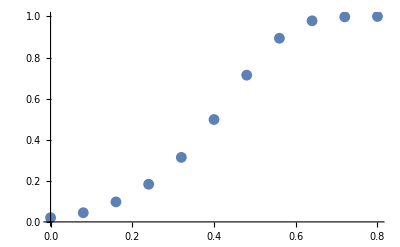

```mathematica
ListPlot[Re@NonAddDat]
```